# Quasi-reversible cyclic voltammetry with coupled homogeneous reaction

## Fully implicit method

This notebook shows how a cyclic voltammogram for the simple quasi-reversible reaction with a coupled chemical reaction

O+e ⇌R
R ⇌_(k_-1)^(k_(+1)) P

can be simulated using implicit finite difference methods.

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
PlotRange->{{upperLimit+1,lowerLimit-1},{-0.55,0.4}},
PlotStyle->{Red,AbsoluteThickness[0.5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["√πχ",FontFamily->  "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make diagonals

```mathematica
Clear[makeCoupledExpDiagonals];

makeCoupledExpDiagonals[m_Integer,d_][a_][khf_,khb_]:=Module[{x,y,z},
x=Table[-a*d*a^(3-2*j)*IdentityMatrix[3],{j,2,m-1}];
z=Table[-d*a^(3-2*j)*IdentityMatrix[3],{j,2,m-2}];
y=Table[(1+(1+a)*d*a^(3-2*j))*IdentityMatrix[3]+{{0,0,0},{0,khf,-khb},{0,-khf,khb}},{j,2,m-1}];
x⟦1,3,3⟧=0;
y⟦1,3,3⟧-=(1+a)^2/(a*(2+a))*d*a^(3-4);
z⟦1,3,3⟧+=1/(a*(2+a))*d*a^(3-4);
{x,y,z}]
```

## Set Up Solution

```mathematica
Clear[tridiagMatSolver];

tridiagMatSolver=Compile[{{x,_Real,3},{y,_Real,3},{z,_Real,3},{b,_Real,2}},Module[{len=Length[b],sol=Table[Table[0.,{Length[b⟦1⟧]}],{Length[b]}],aux,β=Table[Table[0.,{Length[x⟦1⟧]},{Length[x⟦1⟧]}],{Length[b]}],iter=0},

aux=Inverse[y⟦1⟧];
sol⟦1⟧=aux.b⟦1⟧;
Do[β⟦iter⟧=aux.z⟦iter-1⟧;
aux=Inverse[(y⟦iter⟧-x⟦iter⟧.β⟦iter⟧)];
sol⟦iter⟧=aux.(b⟦iter⟧-x⟦iter⟧.sol⟦iter-1⟧),{iter,2,len}]; 			Do[sol⟦iter⟧-=β⟦iter+1⟧.sol⟦iter+1⟧,{iter,len-1,1,-1}];
sol]];
```

```mathematica
Clear[implicitSolveCoupledExp];

implicitSolveCoupledExp[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,khf_,khb_,α_},a_]:=Module[{range,τ,xstar,y1,z1,x,y,z,initial,b2,b3,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1);

{x,y,z}=makeCoupledExpDiagonals[m,d][a][khf,khb];
xstar=x⟦1,{1,2},{1,2}⟧;
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[{1.,0.,0.},{m}];
b2={{1,0},{1,1}};
b3={{(1+a)^2,0},{(1+a)^2,(1+a)^2}};

solveNext[list_List,k_Integer]:=Module[{ξ,b,b1,tmp},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];
y⟦1⟧=y1;
z⟦1⟧=z1;
b=list[[2;;-2]];
b⟦-1⟧+={d*a^(5-2*m),0.,0.};
b1=Inverse[{{a*(2+a)+a*(1+a)*ksStar*ξ^-α,-a*(1+a)*ksStar*ξ^(1.-α)},{a*(2+a),a*(2+a)}}];
y⟦1,{1,2},{1,2}⟧+=xstar.b1.b3;
z⟦1,{1,2},{1,2}⟧-=xstar.b1.b2;
tmp=tridiagMatSolver[x,y,z,b];
Join[{Join[b1.b3.tmp⟦1,{1,2}⟧-b1.b2.tmp⟦2,{1,2}⟧,{((1+a)^2*tmp⟦1,3⟧-tmp⟦2,3⟧)/(a*(2+a))}]},tmp,{{1.,0.,0.}}]
];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Set Constants & variables

```mathematica
Clear[α,𝒟,F,R,T,f];

(*set the value of constants*)

α=0.5(*transfer coefficient, generally taken as being 0.5*);

𝒟=1.*^-5(*diffusion coefficient - assumed to be the same for all species*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature in Kelvin*);

f=F/(R*T);
```

### Set Electrochemical variables

```mathematica
Clear[upperLimit,lowerLimit,𝕥,ksDim];

upperLimit=10.(*initial potential versus the formal potential*);

lowerLimit=-10.(*switching potential versus the formal potential*);

𝕥 =2*(upperLimit+Abs[lowerLimit]);(*the region or range of the sweep*)

ksDim=1.*^1(*dimensionless rate constant*);
```

### Set Simulation Variables

```mathematica
Clear[n,τ,khf,khb,𝔻,a,temp,m,ksStar]

n=Round[𝕥/(0.005*f)];(*5 mV steps*)

τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)

khf=τ*5;(*dimensionless homogeneous forward rate constant*)

khb=τ;(*dimensionless homogeneous backward rate constant*)

𝔻=5.*Max[khb,khf,.4];(*model diffusion coefficient*)

a=1.1;
temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];
m=mm/.temp⟦1⟧//Ceiling;(*number of spacial grid points*)

ksStar=ksDim*Sqrt[(2*𝕥)/(𝔻*(1+a)*(n-1))];(*dimensionless rate constant*)
```

```mathematica
{n,τ,khf,khb,𝔻,m,ksStar,a}
```

{205,0.196078,0.980392,0.196078,4.90196,33,1.9518,1.1}

## Solve it

```mathematica
c=implicitSolveCoupledExp[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,khf,khb,α},a];
```

## Plot CV

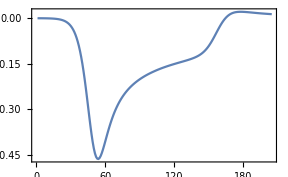

```mathematica
cv1=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c⟦All,All,1⟧];

plot1=ListPlot[cv1,PlotRange->All]
```

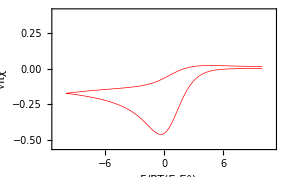

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-(𝕥*(j-1)/(n-1))],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionA]
```